Polynomial Blending

```mathematica
left[s_]:=lb+lm s
right[s_]:=rb+rm (s+(lb-rb+(lm -rm)sMid)/rm)
blend[s_]:=a s^5+b s^4+c s^3+d s^2+e s+f
```

```mathematica
resultBlendAll=Solve[{
blend[0]==left[sMid-sAbs],
blend'[0]==left'[sMid-sAbs],
blend''[0]==left''[sMid-sAbs],
blend[2sAbs]==right[sMid+sAbs],
blend'[2sAbs]==right'[sMid+sAbs],
blend''[2sAbs]==right''[sMid+sAbs],
blend[sAbs]-left[sMid]==maxDiff
},{a,b,c,d,e,f,sAbs}]
```

{{a→0,b→-(27 (lm-rm)^4)/(65536 maxDiff^3),c→-(9 (lm-rm)^3)/(1024 maxDiff^2),d→0,e→lm,f→(3 lb lm+16 lm maxDiff-3 lb rm+3 lm^2 sMid-3 lm rm sMid)/(3 (lm-rm)),sAbs→-(16 maxDiff)/(3 (lm-rm))}}

```mathematica
resultBlend=Solve[{
blend[0]==left[sMid-sAbs],
blend'[0]==left'[sMid-sAbs],
blend''[0]==left''[sMid-sAbs],
blend[2sAbs]==right[sMid+sAbs],
blend'[2sAbs]==right'[sMid+sAbs],
blend''[2sAbs]==right''[sMid+sAbs]
},{a,b,c,d,e,f}]
```

{{a→0,b→-(-lm+rm)/(16 sAbs^3),c→-(lm-rm)/(4 sAbs^2),d→0,e→lm,f→lb-lm sAbs+lm sMid}}

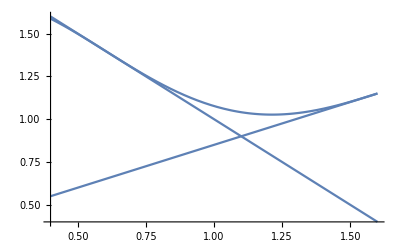

```mathematica
Plot[{
left[s],
right[s],
blend[s]/.resultBlend/.{sAbs->0.5}
}/.{lb->2,lm->-1,sMid->1.1,rb->1,rm->0.5},{s,0.4,1.6}]
```

```mathematica
ToString[Simplify[resultBlend[[1,6,2]]],CForm]
CopyToClipboard[%]
```

lb + lm*(-sAbs + sMid)